## Ex2

```mathematica
A1={{10,0,0,0},{1,8,0,0},{1,-2,2,0},{3,2,-8,1}};
C1={{0,0,-1,5},{0,0,3,0},{0,0,0,-7},{0,0,0,0}};
B1=Inverse[A1].C1//MatrixForm
```

(0 | 0 | -1/10 | 1/2
0 | 0 | 31/80 | -1/16
0 | 0 | 7/16 | -61/16
0 | 0 | 121/40 | -255/8)

```mathematica
Det[({{x, 0, 1/10, -1/2}, {0, x, 31/80, 1/16}, {0, 0, x-7/16, 61/16}, {0, 0, -121/40, x+255/8}})]
```

-(193 x^2)/80+(503 x^3)/16+x^4

```mathematica
FactorSquareFree[-(193 x^2)/80+(503 x^3)/16+x^4]
```

1/80 x^2 (-193+2515 x+80 x^2)

```mathematica
NRoots[1/80 x^2 (-193+2515 x+80 x^2)==0,x]
```

x==-31.5141||x==0.||x==0.||x==0.0765531

```mathematica
Solve[1/80 x^2 (-193+2515 x+80 x^2)==0,x,Complexes]
```

{{x→0},{x→0},{x→1/160 (-2515-33 √5865)},{x→386/(2515+33 √5865)}}

```mathematica
A2={{10,0,0,0},{0,8,0,0},{0,0,2,0},{0,0,0,1}};
C2={{0,0,-1,5},{-1,0,3,0},{-1,2,0,-7},{-3,-2,8,0}};
B2=Inverse[A2].C2;
re=CharacteristicPolynomial[B2,x]
Solve[re==0]
r=Eigenvalues[B2]
```

-27/80+(23 x)/80+(1163 x^2)/40+x^4

{{x→Root-0.113Root[-27+23 #1+2326 #1^2+80 #1^4&,1]-0.11277171394615752},{x→Root0.103Root[-27+23 #1+2326 #1^2+80 #1^4&,2]0.10289141305340493},{x→Root4.94 × 10^-3-5.39 ⅈRoot[-27+23 #1+2326 #1^2+80 #1^4&,3]0.00494015044637629},{x→Root4.94 × 10^-3+5.39 ⅈRoot[-27+23 #1+2326 #1^2+80 #1^4&,4]0.00494015044637629}}

```mathematica
N[{{x->Root[-27+23 #1+2326 #1^2+80 #1^4&,1,0]},{x->Root[-27+23 #1+2326 #1^2+80 #1^4&,2,0]},{x->Root[-27+23 #1+2326 #1^2+80 #1^4&,3,0]},{x->Root[-27+23 #1+2326 #1^2+80 #1^4&,4,0]}}]
```

{{x→-0.112772},{x→0.102891},{x→0.00494015-5.39321 ⅈ},{x→0.00494015+5.39321 ⅈ}}

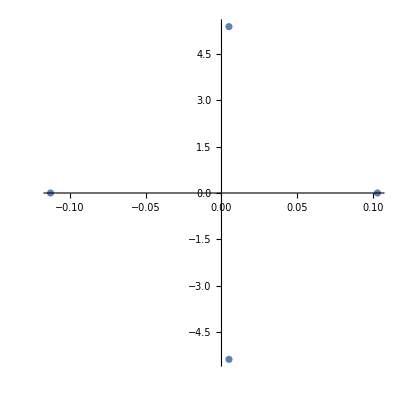

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@r,AspectRatio->1]
```

## EX3

```mathematica
D3={{4,0,0},{0,4,0},{0,0,4}};
L3={{0,0,0},{-1,0,0},{-1,-1,0}};
U3={{0,-1,-1},{0,0,-1},{0,0,0}};
Lw=Inverse[D3-w L3].((1-w)D3+w U3)//MatrixForm
```

(1-w | -w/4 | -w/4
-1/4 (1-w) w | 1-w+w^2/16 | -w/4+w^2/16
1/16 (1-w) (-4 w+w^2) | -1/4 (1-w) w-1/64 w (-4 w+w^2) | 1-w+w^2/16-1/64 w (-4 w+w^2))

```mathematica
b3={{4},{-2},{-2}};
f3=w Inverse[D3-w L3].b3//MatrixForm
```

(w
(-1/2-w/4) w
w (-1/2+w/8+1/16 (-4 w+w^2)))

## EX4

```mathematica
D4={{15,0,0},{0,8,0},{0,0,20}};
L4={{0,0,0},{3,0,0},{-2,-1,0}};
U4={{0,3,-2},{0,0,-1},{0,0,0}};
b4={{14},{6},{23}};
B4=Inverse[D4-L4].U4//MatrixForm
fgs4=Inverse[D4-L4].b4//MatrixForm
Lw4=Inverse[D4-w L4].((1-w)D4+w U4)//MatrixForm

f4=w Inverse[D4-w L4].b4//MatrixForm
```

(0 | 1/5 | -2/15
0 | 3/40 | -7/40
0 | -19/800 | 53/2400)

(14/15
11/10
601/600)

(1-w | w/5 | -(2 w)/15
3/8 (1-w) w | 1-w+(3 w^2)/40 | -w/8-w^2/20
1/160 (1-w) (-16 w-3 w^2) | -1/20 (1-w) w+1/800 w (-16 w-3 w^2) | 1-w+w^2/160-(w (-16 w-3 w^2))/1200)

((14 w)/15
(3/4+(7 w)/20) w
w (23/20-(3 w)/80+(7 (-16 w-3 w^2))/1200))